“Not really FM, but a waveshaper”

```mathematica
Plot[{Tanh[x],If[Abs[x]≥1,Sign[x]1,x]},{x,-3,3}]
```

Syntax::tsntxi: "NotreallyFM,butawaveshaper" is incomplete; more input is needed.

The classic FM example Plot

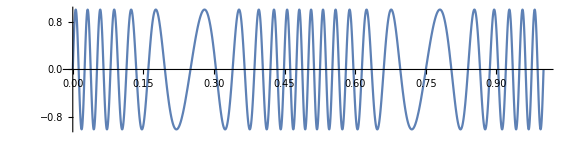

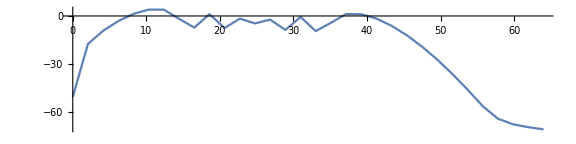

```mathematica
sr=128;
Plot[Sin[2Pi 24 t+8Sin[2Pi 2t]]//N,{t,0,1},AspectRatio->1/4,ImageSize->Large]
Periodogram[Table[Sin[2Pi 24 t+8Sin[2Pi 2t]]//N,{t,0,1-1/sr,1/sr}],64,32,HammingWindow,PlotRange->All,SampleRate->sr,AspectRatio->1/4,ImageSize->Large]
```

Now we get to FM synthesis

```mathematica
sr=16000;t=1/sr;
fb=330;
fmod=.3*fb;
modi=0.10;
mod[f_,x_]:=SawtoothWave[f x];
modSin[f_,x_]:=Sin[f 2Pi x];
Manipulate[{
a=Table[Sin[fb 2Pi x +x modi modSin[fmod,x] ],{x,0,5-t,t}];
ListLinePlot[a[[1;;Floor[sr/fb]]],AspectRatio->1/4,ImageSize->Large]
Periodogram[a,1028,512,HammingWindow,SampleRate->sr,AspectRatio->1/4,ImageSize->Large,PlotRange->{{Automatic,Automatic},{-60,20}},Frame->True]},{modi,0,10}]
```

```mathematica
ListPlay[a,SampleRate->sr]
```

-Graphics-